```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
<<"MaTeX`"
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Click here for documentation on configuring MaTeX.

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.5, la->1.5};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

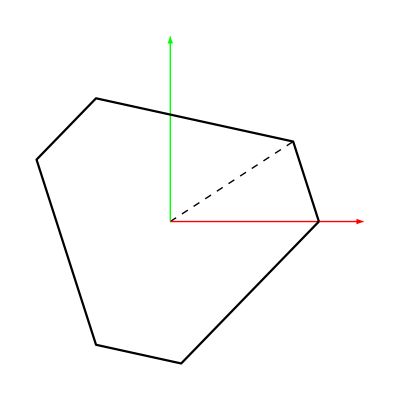

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

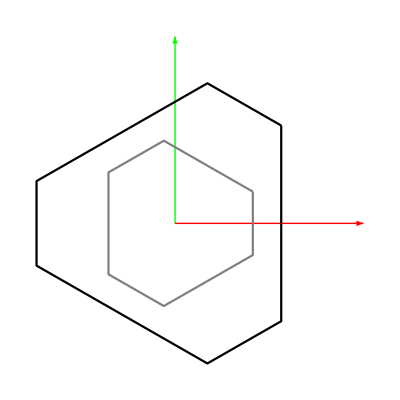

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Equating both the points*)
```

```mathematica
eq1 = (ag - bdat);
```

```mathematica
lsample = Inner[Rule, l/.qrule, Table[√(eq1[[i]].eq1[[i]]), {i, 6}], List]
```

{l1[t]→1.20833,l2[t]→1.20833,l3[t]→1.20833,l4[t]→1.20833,l5[t]→1.20833,l6[t]→1.20833}

```mathematica
eq2 = ag - a/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.lsample;
```

```mathematica
(*Considering one of the solutions for Cos in this case taking the first one. This gives the solutions for all the ψ's*)
```

```mathematica
ψt = ψ/.qrule;
ϕt = ϕ/.qrule;
```

```mathematica
ψsample = Flatten[Table[(ψt[[i]]-> ArcTan[Cos[ψt[[i]]], Sin[ψt[[i]]]]/.{Cos[ψt[[i]]]-> √(1-Sin[ψt[[i]]]^2)}/.Solve[eq2[[i]][[2]]==0, Sin[ψt[[i]]]]),{i, 6}]]
```

{ψ1[t]→0.390648,ψ2[t]→0.337095,ψ3[t]→-0.0500618,ψ4[t]→0.0500618,ψ5[t]→-0.337095,ψ6[t]→-0.390648}

```mathematica
ϕsample = Table[ϕt[[i]]-> ArcTan[Cos[ϕt[[i]]], Sin[ϕt[[i]]]]/.Flatten[{Solve[((eq2/.ψsample)[[i]][[1]])==0, Sin[ϕt[[i]]]], Solve[((eq2/.ψsample)[[i]][[3]])==0, Cos[ϕt[[i]]]]}],{i, 6}]
```

{ϕ1[t]→-0.17618,ϕ2[t]→-0.266725,ϕ3[t]→0.423902,ϕ4[t]→0.423902,ϕ5[t]→-0.266725,ϕ6[t]→-0.17618}

```mathematica
sampledat = Join[ϕsample, ψsample, lsample]
```

{ϕ1[t]→-0.17618,ϕ2[t]→-0.266725,ϕ3[t]→0.423902,ϕ4[t]→0.423902,ϕ5[t]→-0.266725,ϕ6[t]→-0.17618,ψ1[t]→0.390648,ψ2[t]→0.337095,ψ3[t]→-0.0500618,ψ4[t]→0.0500618,ψ5[t]→-0.337095,ψ6[t]→-0.390648,l1[t]→1.20833,l2[t]→1.20833,l3[t]→1.20833,l4[t]→1.20833,l5[t]→1.20833,l6[t]→1.20833}

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
ηconfig = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
ηconfig//Dimensions
```

{12}

```mathematica
ηeqn = ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.sampledat
```

{6.10623×10^-16,8.88178×10^-16,7.21645×10^-16,1.77636×10^-15,-2.22045×10^-16,0.,8.88178×10^-16,4.44089×10^-16,4.44089×10^-16,-1.59595×10^-16,-7.91034×10^-16,-3.46945×10^-16}

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}];(*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*Make sure the denominator is not zero. Which is not possible for any real values*)
```

```mathematica
Denominator[Together[ηeqn/.lsample/.htanrule]]
```

{(1.+p1^2) (1.+p2^2) (1.+s1^2) (1.+s2^2),(1.+p2^2) (1.+p3^2) (1.+s2^2) (1.+s3^2),(1.+p3^2) (1.+p4^2) (1.+s3^2) (1.+s4^2),(1.+p4^2) (1.+p5^2) (1.+s4^2) (1.+s5^2),(1.+p5^2) (1.+p6^2) (1.+s5^2) (1.+s6^2),(1.+p1^2) (1.+p6^2) (1.+s1^2) (1.+s6^2),(1.+p1^2) (1.+p3^2) (1.+s1^2) (1.+s3^2),(1.+p1^2) (1.+p4^2) (1.+s1^2) (1.+s4^2),(1.+p1^2) (1.+p5^2) (1.+s1^2) (1.+s5^2),(1.+p1^2) (1.+p2^2) (1.+p3^2) (1.+p4^2) (1.+s1^2) (1.+s2^2) (1.+s3^2) (1.+s4^2),(1.+p1^2) (1.+p3^2) (1.+p4^2) (1.+p5^2) (1.+s1^2) (1.+s3^2) (1.+s4^2) (1.+s5^2),(1.+p1^2) (1.+p4^2) (1.+p5^2) (1.+p6^2) (1.+s1^2) (1.+s4^2) (1.+s5^2) (1.+s6^2)}

```mathematica
ηeqnlist = Numerator[Together[ηeqn/.lsample/.htanrule]]
```

{-0.156882 (1.-15.6931 p1-36.2269 p1^2+15.6931 p2+74.4538 p1 p2+15.6931 p1^2 p2-36.2269 p2^2-15.6931 p1 p2^2+57+1. s1^2 s2^2+15.6931 p1 s1^2 s2^2-36.2269 p1^2 s1^2 s2^2-15.6931 p2 s1^2 s2^2+74.4538 p1 p2 s1^2 s2^2-15.6931 p1^2 p2 s1^2 s2^2-36.2269 p2^2 s1^2 s2^2+15.6931 p1 p2^2 s1^2 s2^2+1. p1^2 p2^2 s1^2 s2^2),1.65873 (1),8,1,-2.22045×10^-16 p1+1.67582 p1^2+2347+1.67582 p4^2 p5^2 p6^2 s1^2 s4^2 s5^2 s6^2+2.22045×10^-16 p1 p4^2 p5^2 p6^2 s1^2 s4^2 s5^2 s6^2}
 |  |  |  |

```mathematica
ηeqnlist[[12]]//Chop//Simplify
```

5.554625889137231*p5^2 + 5.692888764381626*p5^2*p6 - 5.554625889137231*p6^2 - 5.692888764381626*p5*p6^2 - 9.860372581746985*p5^2*s1 - 14.113815474764762*p5^2*p6*s1 + 
  6.885517008617473*p6^2*s1 + 14.113815474764762*p5*p6^2*s1 - 2.974855573129514*p5^2*p6^2*s1 + 1.6758200205880798*s1^2 - 2.257821432488463*p5*s1^2 + 7.230445909725311*p5^2*s1^2 + 
  3.975355098435044*p6*s1^2 + 9.668243862816672*p5^2*p6*s1^2 - 3.878805868549152*p6^2*s1^2 - 7.950710196870091*p5*p6^2*s1^2 + 1.6758200205880796*p5^2*p6^2*s1^2 + 
  14.113815474764762*p5^2*p6*s4 + 2.9748555731295148*p6^2*s4 - 14.113815474764762*p5*p6^2*s4 + 2.974855573129514*p5^2*p6^2*s4 - 2.974855573129514*s1^2*s4 + 
  14.113815474764762*p5*s1^2*s4 - 2.9748555731295148*p5^2*s1^2*s4 - 14.113815474764762*p6*s1^2*s4 - 1.6758200205880796*s4^2 + 7.950710196870091*p5*s4^2 + 3.878805868549152*p5^2*s4^2 - 
  9.668243862816672*p6*s4^2 - 3.975355098435044*p5^2*p6*s4^2 - 7.230445909725311*p6^2*s4^2 + 2.257821432488463*p5*p6^2*s4^2 - 1.6758200205880798*p5^2*p6^2*s4^2 + 
  2.974855573129514*s1*s4^2 - 14.113815474764762*p5*s1*s4^2 - 6.885517008617473*p5^2*s1*s4^2 + 14.113815474764762*p6*s1*s4^2 + 9.860372581746985*p6^2*s1*s4^2 + 
  5.692888764381626*p5*s1^2*s4^2 + 5.554625889137231*p5^2*s1^2*s4^2 - 5.692888764381626*p6*s1^2*s4^2 - 5.554625889137231*p6^2*s1^2*s4^2 - 9.860372581746988*p6^2*s5 - 
  9.860372581746988*p5^2*p6^2*s5 + 9.860372581746986*s1^2*s5 + 9.860372581746986*p5^2*s1^2*s5 + 14.113815474764762*p6*s1^2*s5 + 14.113815474764762*p5^2*p6*s1^2*s5 - 
  14.113815474764762*p6*s4^2*s5 - 14.113815474764762*p5^2*p6*s4^2*s5 - 9.860372581746986*p6^2*s4^2*s5 - 9.860372581746986*p5^2*p6^2*s4^2*s5 + 9.860372581746988*s1^2*s4^2*s5 + 
  9.860372581746988*p5^2*s1^2*s4^2*s5 + 5.554625889137231*s5^2 + 5.692888764381626*p6*s5^2 + 5.692888764381626*p5*p6^2*s5^2 - 5.554625889137231*p5^2*p6^2*s5^2 - 
  9.860372581746985*s1*s5^2 - 14.113815474764762*p6*s1*s5^2 - 2.974855573129514*p6^2*s1*s5^2 - 14.113815474764762*p5*p6^2*s1*s5^2 + 6.885517008617473*p5^2*p6^2*s1*s5^2 + 
  7.230445909725311*s1^2*s5^2 + 2.257821432488463*p5*s1^2*s5^2 + 1.6758200205880798*p5^2*s1^2*s5^2 + 9.668243862816672*p6*s1^2*s5^2 + 3.975355098435044*p5^2*p6*s1^2*s5^2 + 
  1.6758200205880796*p6^2*s1^2*s5^2 + 7.950710196870091*p5*p6^2*s1^2*s5^2 - 3.878805868549152*p5^2*p6^2*s1^2*s5^2 + 14.113815474764762*p6*s4*s5^2 + 2.974855573129514*p6^2*s4*s5^2 + 
  14.113815474764762*p5*p6^2*s4*s5^2 + 2.9748555731295148*p5^2*p6^2*s4*s5^2 - 2.9748555731295148*s1^2*s4*s5^2 - 14.113815474764762*p5*s1^2*s4*s5^2 - 2.974855573129514*p5^2*s1^2*s4*s5^2 - 
  14.113815474764762*p5^2*p6*s1^2*s4*s5^2 + 3.878805868549152*s4^2*s5^2 - 7.950710196870091*p5*s4^2*s5^2 - 1.6758200205880796*p5^2*s4^2*s5^2 - 3.975355098435044*p6*s4^2*s5^2 - 
  9.668243862816672*p5^2*p6*s4^2*s5^2 - 1.6758200205880798*p6^2*s4^2*s5^2 - 2.257821432488463*p5*p6^2*s4^2*s5^2 - 7.230445909725311*p5^2*p6^2*s4^2*s5^2 - 6.885517008617473*s1*s4^2*s5^2 + 
  14.113815474764762*p5*s1*s4^2*s5^2 + 2.974855573129514*p5^2*s1*s4^2*s5^2 + 14.113815474764762*p5^2*p6*s1*s4^2*s5^2 + 9.860372581746985*p5^2*p6^2*s1*s4^2*s5^2 + 
  5.554625889137231*s1^2*s4^2*s5^2 - 5.692888764381626*p5*s1^2*s4^2*s5^2 - 5.692888764381626*p5^2*p6*s1^2*s4^2*s5^2 - 5.554625889137231*p5^2*p6^2*s1^2*s4^2*s5^2 + 
  9.860372581746986*p5^2*s6 + 9.860372581746986*p5^2*p6^2*s6 - 6.885517008617473*s1^2*s6 - 14.113815474764762*p5*s1^2*s6 + 2.9748555731295143*p5^2*s1^2*s6 - 
  6.885517008617473*p6^2*s1^2*s6 - 14.113815474764762*p5*p6^2*s1^2*s6 + 2.9748555731295143*p5^2*p6^2*s1^2*s6 - 2.9748555731295143*s4^2*s6 + 14.113815474764762*p5*s4^2*s6 + 
  6.885517008617473*p5^2*s4^2*s6 - 2.9748555731295143*p6^2*s4^2*s6 + 14.113815474764762*p5*p6^2*s4^2*s6 + 6.885517008617473*p5^2*p6^2*s4^2*s6 - 9.860372581746986*s1^2*s4^2*s6 - 
  9.860372581746986*p6^2*s1^2*s4^2*s6 + 9.860372581746986*s5^2*s6 + 9.860372581746986*p6^2*s5^2*s6 + 2.9748555731295143*s1^2*s5^2*s6 + 14.113815474764762*p5*s1^2*s5^2*s6 - 
  6.885517008617473*p5^2*s1^2*s5^2*s6 + 2.9748555731295143*p6^2*s1^2*s5^2*s6 + 14.113815474764762*p5*p6^2*s1^2*s5^2*s6 - 6.885517008617473*p5^2*p6^2*s1^2*s5^2*s6 + 
  6.885517008617473*s4^2*s5^2*s6 - 14.113815474764762*p5*s4^2*s5^2*s6 - 2.9748555731295143*p5^2*s4^2*s5^2*s6 + 6.885517008617473*p6^2*s4^2*s5^2*s6 - 
  14.113815474764762*p5*p6^2*s4^2*s5^2*s6 - 2.9748555731295143*p5^2*p6^2*s4^2*s5^2*s6 - 9.860372581746986*p5^2*s1^2*s4^2*s5^2*s6 - 9.860372581746986*p5^2*p6^2*s1^2*s4^2*s5^2*s6 - 
  5.554625889137231*s6^2 - 5.692888764381626*p5*s6^2 - 5.692888764381626*p5^2*p6*s6^2 + 5.554625889137231*p5^2*p6^2*s6^2 + 6.885517008617473*s1*s6^2 + 14.113815474764762*p5*s1*s6^2 - 
  2.974855573129514*p5^2*s1*s6^2 + 14.113815474764762*p5^2*p6*s1*s6^2 - 9.860372581746985*p5^2*p6^2*s1*s6^2 - 3.878805868549152*s1^2*s6^2 - 7.950710196870091*p5*s1^2*s6^2 + 
  1.6758200205880796*p5^2*s1^2*s6^2 - 3.975355098435044*p6*s1^2*s6^2 - 9.668243862816672*p5^2*p6*s1^2*s6^2 + 1.6758200205880798*p6^2*s1^2*s6^2 - 2.257821432488463*p5*p6^2*s1^2*s6^2 + 
  7.230445909725311*p5^2*p6^2*s1^2*s6^2 + 2.9748555731295148*s4*s6^2 - 14.113815474764762*p5*s4*s6^2 + 2.974855573129514*p5^2*s4*s6^2 - 14.113815474764762*p5^2*p6*s4*s6^2 + 
  14.113815474764762*p6*s1^2*s4*s6^2 - 2.974855573129514*p6^2*s1^2*s4*s6^2 + 14.113815474764762*p5*p6^2*s1^2*s4*s6^2 - 2.9748555731295148*p5^2*p6^2*s1^2*s4*s6^2 - 
  7.230445909725311*s4^2*s6^2 + 2.257821432488463*p5*s4^2*s6^2 - 1.6758200205880798*p5^2*s4^2*s6^2 + 9.668243862816672*p6*s4^2*s6^2 + 3.975355098435044*p5^2*p6*s4^2*s6^2 - 
  1.6758200205880796*p6^2*s4^2*s6^2 + 7.950710196870091*p5*p6^2*s4^2*s6^2 + 3.878805868549152*p5^2*p6^2*s4^2*s6^2 + 9.860372581746985*s1*s4^2*s6^2 - 14.113815474764762*p6*s1*s4^2*s6^2 + 
  2.974855573129514*p6^2*s1*s4^2*s6^2 - 14.113815474764762*p5*p6^2*s1*s4^2*s6^2 - 6.885517008617473*p5^2*p6^2*s1*s4^2*s6^2 - 5.554625889137231*s1^2*s4^2*s6^2 + 
  5.692888764381626*p6*s1^2*s4^2*s6^2 + 5.692888764381626*p5*p6^2*s1^2*s4^2*s6^2 + 5.554625889137231*p5^2*p6^2*s1^2*s4^2*s6^2 - 9.860372581746988*s5*s6^2 - 
  9.860372581746988*p5^2*s5*s6^2 - 14.113815474764762*p6*s1^2*s5*s6^2 - 14.113815474764762*p5^2*p6*s1^2*s5*s6^2 + 9.860372581746986*p6^2*s1^2*s5*s6^2 + 
  9.860372581746986*p5^2*p6^2*s1^2*s5*s6^2 - 9.860372581746986*s4^2*s5*s6^2 - 9.860372581746986*p5^2*s4^2*s5*s6^2 + 14.113815474764762*p6*s4^2*s5*s6^2 + 
  14.113815474764762*p5^2*p6*s4^2*s5*s6^2 + 9.860372581746988*p6^2*s1^2*s4^2*s5*s6^2 + 9.860372581746988*p5^2*p6^2*s1^2*s4^2*s5*s6^2 + 5.692888764381626*p5*s5^2*s6^2 - 
  5.554625889137231*p5^2*s5^2*s6^2 - 5.692888764381626*p6*s5^2*s6^2 + 5.554625889137231*p6^2*s5^2*s6^2 - 2.974855573129514*s1*s5^2*s6^2 - 14.113815474764762*p5*s1*s5^2*s6^2 + 
  6.885517008617473*p5^2*s1*s5^2*s6^2 + 14.113815474764762*p6*s1*s5^2*s6^2 - 9.860372581746985*p6^2*s1*s5^2*s6^2 + 1.6758200205880796*s1^2*s5^2*s6^2 + 
  7.950710196870091*p5*s1^2*s5^2*s6^2 - 3.878805868549152*p5^2*s1^2*s5^2*s6^2 - 9.668243862816672*p6*s1^2*s5^2*s6^2 - 3.975355098435044*p5^2*p6*s1^2*s5^2*s6^2 + 
  7.230445909725311*p6^2*s1^2*s5^2*s6^2 + 2.257821432488463*p5*p6^2*s1^2*s5^2*s6^2 + 1.6758200205880798*p5^2*p6^2*s1^2*s5^2*s6^2 + 2.974855573129514*s4*s5^2*s6^2 + 
  14.113815474764762*p5*s4*s5^2*s6^2 + 2.9748555731295148*p5^2*s4*s5^2*s6^2 - 14.113815474764762*p6*s4*s5^2*s6^2 + 14.113815474764762*p5^2*p6*s1^2*s4*s5^2*s6^2 - 
  2.9748555731295148*p6^2*s1^2*s4*s5^2*s6^2 - 14.113815474764762*p5*p6^2*s1^2*s4*s5^2*s6^2 - 2.974855573129514*p5^2*p6^2*s1^2*s4*s5^2*s6^2 - 1.6758200205880798*s4^2*s5^2*s6^2 - 
  2.257821432488463*p5*s4^2*s5^2*s6^2 - 7.230445909725311*p5^2*s4^2*s5^2*s6^2 + 3.975355098435044*p6*s4^2*s5^2*s6^2 + 9.668243862816672*p5^2*p6*s4^2*s5^2*s6^2 + 
  3.878805868549152*p6^2*s4^2*s5^2*s6^2 - 7.950710196870091*p5*p6^2*s4^2*s5^2*s6^2 - 1.6758200205880796*p5^2*p6^2*s4^2*s5^2*s6^2 + 9.860372581746985*p5^2*s1*s4^2*s5^2*s6^2 - 
  14.113815474764762*p5^2*p6*s1*s4^2*s5^2*s6^2 - 6.885517008617473*p6^2*s1*s4^2*s5^2*s6^2 + 14.113815474764762*p5*p6^2*s1*s4^2*s5^2*s6^2 + 2.974855573129514*p5^2*p6^2*s1*s4^2*s5^2*s6^2 - 
  5.554625889137231*p5^2*s1^2*s4^2*s5^2*s6^2 + 5.692888764381626*p5^2*p6*s1^2*s4^2*s5^2*s6^2 + 5.554625889137231*p6^2*s1^2*s4^2*s5^2*s6^2 - 
  5.692888764381626*p5*p6^2*s1^2*s4^2*s5^2*s6^2 + p4*(-1.717533665946581*s1^2 + 1.717533665946581*s1^2*s4^2 - 14.113815474764762*s1^2*s5 + 14.113815474764762*s1^2*s4^2*s5 - 
    7.950710196870089*s5^2 + 14.113815474764762*s1*s5^2 - 9.66824386281667*s1^2*s5^2 + 7.950710196870089*s4^2*s5^2 - 14.113815474764762*s1*s4^2*s5^2 + 9.66824386281667*s1^2*s4^2*s5^2 + 
    14.113815474764762*s1^2*s6 - 14.113815474764762*s1^2*s4^2*s6 - 14.113815474764762*s5^2*s6 + 14.113815474764762*s4^2*s5^2*s6 + 9.66824386281667*s6^2 - 14.113815474764762*s1*s6^2 + 
    7.950710196870089*s1^2*s6^2 - 9.66824386281667*s4^2*s6^2 + 14.113815474764762*s1*s4^2*s6^2 - 7.950710196870089*s1^2*s4^2*s6^2 + 14.113815474764762*s5*s6^2 - 
    14.113815474764762*s4^2*s5*s6^2 + 1.717533665946581*s5^2*s6^2 - 1.717533665946581*s4^2*s5^2*s6^2 + 
    p6^2*(9.66824386281667 + 14.113815474764762*s5 + 1.717533665946581*s5^2 - 14.113815474764762*s5^2*s6 - 7.950710196870089*s5^2*s6^2 + 
      s4^2*(-9.66824386281667 - 14.113815474764762*s5 + s5^2*(-1.717533665946581 + 14.113815474764762*s6 + 7.950710196870089*s6^2)) + 
      s1*(-14.113815474764762 + 14.113815474764762*s5^2*s6^2 + s4^2*(14.113815474764762 - 14.113815474764762*s5^2*s6^2)) + 
      s1^2*(7.950710196870089 + 14.113815474764762*s6 + (-1.717533665946581 - 14.113815474764762*s5 - 9.66824386281667*s5^2)*s6^2 + 
        s4^2*(-7.950710196870089 - 14.113815474764762*s6 + (1.717533665946581 + 14.113815474764762*s5 + 9.66824386281667*s5^2)*s6^2))) + 
    p5^2*(-7.950710196870089 + 7.950710196870089*s4^2 - 14.113815474764762*s6 + 14.113815474764762*s4^2*s6 + 1.717533665946581*s6^2 - 1.717533665946581*s4^2*s6^2 + 
      14.113815474764762*s5*s6^2 - 14.113815474764762*s4^2*s5*s6^2 + 9.66824386281667*s5^2*s6^2 - 9.66824386281667*s4^2*s5^2*s6^2 + 
      s1*(14.113815474764762 - 14.113815474764762*s5^2*s6^2 + s4^2*(-14.113815474764762 + 14.113815474764762*s5^2*s6^2)) + 
      s1^2*(-9.66824386281667 - 14.113815474764762*s5 + s5^2*(-1.717533665946581 + 14.113815474764762*s6 + 7.950710196870089*s6^2) + 
        s4^2*(9.66824386281667 + 14.113815474764762*s5 + s5^2*(1.717533665946581 - 14.113815474764762*s6 - 7.950710196870089*s6^2))) + 
      p6^2*(1.717533665946581 - 14.113815474764762*s6 - 7.950710196870089*s6^2 + 14.113815474764762*s1*s6^2 - 9.66824386281667*s1^2*s6^2 + 
        s5*(14.113815474764762 - 14.113815474764762*s1^2*s6^2) + s5^2*(9.66824386281667 - 14.113815474764762*s1 + s1^2*(7.950710196870089 + 14.113815474764762*s6 - 
            1.717533665946581*s6^2)) + s4^2*(-1.717533665946581 + 14.113815474764762*s6 + (7.950710196870089 - 14.113815474764762*s1 + 9.66824386281667*s1^2)*s6^2 + 
          s5*(-14.113815474764762 + 14.113815474764762*s1^2*s6^2) + s5^2*(-9.66824386281667 + 14.113815474764762*s1 + s1^2*(-7.950710196870089 - 14.113815474764762*s6 + 
              1.717533665946581*s6^2)))))) + p4^2*(-1.6758200205880796 + 2.974855573129514*s1 - 2.974855573129514*s1^2*s4 + 1.6758200205880798*s1^2*s4^2 + 9.860372581746988*s1^2*s5 + 
    9.860372581746986*s1^2*s4^2*s5 + 3.878805868549152*s5^2 - 6.885517008617473*s1*s5^2 + 5.554625889137231*s1^2*s5^2 - 2.9748555731295148*s1^2*s4*s5^2 + 5.554625889137231*s4^2*s5^2 - 
    9.860372581746985*s1*s4^2*s5^2 + 7.230445909725311*s1^2*s4^2*s5^2 - 2.9748555731295143*s6 - 9.860372581746986*s1^2*s6 - 6.885517008617473*s1^2*s4^2*s6 + 6.885517008617473*s5^2*s6 + 
    9.860372581746986*s4^2*s5^2*s6 + 2.9748555731295143*s1^2*s4^2*s5^2*s6 - 7.230445909725311*s6^2 + 9.860372581746985*s1*s6^2 - 5.554625889137231*s1^2*s6^2 + 
    2.9748555731295148*s4*s6^2 - 5.554625889137231*s4^2*s6^2 + 6.885517008617473*s1*s4^2*s6^2 - 3.878805868549152*s1^2*s4^2*s6^2 - 9.860372581746986*s5*s6^2 - 
    9.860372581746988*s4^2*s5*s6^2 - 1.6758200205880798*s5^2*s6^2 + 2.974855573129514*s4*s5^2*s6^2 - 2.974855573129514*s1*s4^2*s5^2*s6^2 + 1.6758200205880796*s1^2*s4^2*s5^2*s6^2 + 
    p6*(-9.668243862816672 + 9.668243862816672*s6^2 + s5*(-14.113815474764762 + 14.113815474764762*s6^2) + 
      s5^2*(-3.975355098435044 + 3.975355098435044*s6^2 + s4*(14.113815474764762 - 14.113815474764762*s6^2) + s4^2*(5.692888764381626 - 5.692888764381626*s6^2)) + 
      s1*(14.113815474764762 - 14.113815474764762*s6^2 + s4^2*s5^2*(-14.113815474764762 + 14.113815474764762*s6^2)) + 
      s1^2*(-5.692888764381626 + 5.692888764381626*s6^2 + s4*(-14.113815474764762 + 14.113815474764762*s6^2) + 
        s4^2*(3.975355098435044 - 3.975355098435044*s6^2 + s5*(14.113815474764762 - 14.113815474764762*s6^2) + s5^2*(9.668243862816672 - 9.668243862816672*s6^2)))) + 
    p6^2*(-7.230445909725311 - 9.860372581746986*s5 - 1.6758200205880798*s5^2 + s4*(2.9748555731295148 + 2.974855573129514*s5^2) - 2.9748555731295143*s6 + 6.885517008617473*s5^2*s6 - 
      1.6758200205880796*s6^2 + 3.878805868549152*s5^2*s6^2 + s4^2*(-5.554625889137231 - 9.860372581746988*s5 + s5^2*s6*(9.860372581746986 + 5.554625889137231*s6)) + 
      s1*(9.860372581746985 + (2.974855573129514 - 6.885517008617473*s5^2)*s6^2 + s4^2*(6.885517008617473 + s5^2*(-2.974855573129514 - 9.860372581746985*s6^2))) + 
      s1^2*(-5.554625889137231 - 9.860372581746986*s6 + s5*(9.860372581746988 + 5.554625889137231*s5)*s6^2 + s4*(-2.974855573129514 - 2.9748555731295148*s5^2)*s6^2 + 
        s4^2*(-3.878805868549152 - 6.885517008617473*s6 + 1.6758200205880798*s6^2 + 9.860372581746986*s5*s6^2 + s5^2*(1.6758200205880796 + 2.9748555731295143*s6 + 
            7.230445909725311*s6^2)))) + p5^2*(3.878805868549152 + 5.554625889137231*s4^2 - 1.6758200205880796*s5^2 + 6.885517008617473*s6 + 9.860372581746986*s4^2*s6 - 
      2.9748555731295143*s5^2*s6 - 1.6758200205880798*s6^2 + 2.974855573129514*s4*s6^2 - 9.860372581746986*s5*s6^2 - 9.860372581746988*s4^2*s5*s6^2 - 7.230445909725311*s5^2*s6^2 + 
      2.9748555731295148*s4*s5^2*s6^2 - 5.554625889137231*s4^2*s5^2*s6^2 + s1*(-6.885517008617473 + s5^2*(2.974855573129514 + 9.860372581746985*s6^2) + 
        s4^2*(-9.860372581746985 + (-2.974855573129514 + 6.885517008617473*s5^2)*s6^2)) + s1^2*(5.554625889137231 + 9.860372581746988*s5 + 
        s4*(-2.9748555731295148 - 2.974855573129514*s5^2) + s5^2*(-9.860372581746986 - 5.554625889137231*s6)*s6 + 
        s4^2*(7.230445909725311 + 9.860372581746986*s5 + 2.9748555731295143*s6 + 1.6758200205880796*s6^2 + s5^2*(1.6758200205880798 - 6.885517008617473*s6 - 3.878805868549152*s6^2))) + 
      p6*(-3.975355098435044 + 3.975355098435044*s6^2 + s5*(-14.113815474764762 + 14.113815474764762*s6^2) + 
        s5^2*(-9.668243862816672 + 9.668243862816672*s6^2 + s1*(14.113815474764762 - 14.113815474764762*s6^2) + s1^2*(-5.692888764381626 + 5.692888764381626*s6^2)) + 
        s4*(14.113815474764762 - 14.113815474764762*s6^2 + s1^2*s5^2*(-14.113815474764762 + 14.113815474764762*s6^2)) + 
        s4^2*(5.692888764381626 - 5.692888764381626*s6^2 + s1*(-14.113815474764762 + 14.113815474764762*s6^2) + s1^2*(9.668243862816672 - 9.668243862816672*s6^2 + 
            s5*(14.113815474764762 - 14.113815474764762*s6^2) + s5^2*(3.975355098435044 - 3.975355098435044*s6^2)))) + 
      p6^2*(-1.6758200205880798 + 6.885517008617473*s6 + 3.878805868549152*s6^2 - 6.885517008617473*s1*s6^2 + 5.554625889137231*s1^2*s6^2 + 
        s5*(-9.860372581746986 + 9.860372581746988*s1^2*s6^2) + s5^2*(-7.230445909725311 + s1^2*(-5.554625889137231 - 9.860372581746986*s6) - 2.9748555731295143*s6 - 
          1.6758200205880796*s6^2 + s1*(9.860372581746985 + 2.974855573129514*s6^2)) + s4*(2.974855573129514 - 2.9748555731295148*s1^2*s6^2 + 
          s5^2*(2.9748555731295148 - 2.974855573129514*s1^2*s6^2)) + s4^2*(-9.860372581746988*s5 - 5.554625889137231*s5^2 + s6*(9.860372581746986 + 5.554625889137231*s6) + 
          s1*(-2.974855573129514 + 6.885517008617473*s5^2 - 9.860372581746985*s6^2) + s1^2*(1.6758200205880796 + 2.9748555731295143*s6 + 7.230445909725311*s6^2 + 
            9.860372581746986*s5*s6^2 + s5^2*(-3.878805868549152 - 6.885517008617473*s6 + 1.6758200205880798*s6^2))))) + 
    p5*(7.950710196870091 - 7.950710196870091*s5^2 + 14.113815474764762*s6 - 14.113815474764762*s5^2*s6 + 2.257821432488463*s6^2 - 14.113815474764762*s4*s6^2 - 
      5.692888764381626*s4^2*s6^2 - 2.257821432488463*s5^2*s6^2 + 14.113815474764762*s4*s5^2*s6^2 + 5.692888764381626*s4^2*s5^2*s6^2 + 
      s1*(-14.113815474764762 + 14.113815474764762*s4^2*s6^2 + s5^2*(14.113815474764762 - 14.113815474764762*s4^2*s6^2)) + 
      s1^2*(5.692888764381626 - 5.692888764381626*s5^2 + s4*(14.113815474764762 - 14.113815474764762*s5^2) + s4^2*(-2.257821432488463 - 14.113815474764762*s6 - 7.950710196870091*s6^2 + 
          s5^2*(2.257821432488463 + 14.113815474764762*s6 + 7.950710196870091*s6^2))) + p6^2*(2.257821432488463 + 14.113815474764762*s6 + 7.950710196870091*s6^2 - 
        14.113815474764762*s1*s6^2 + 5.692888764381626*s1^2*s6^2 + s5^2*(-2.257821432488463 - 14.113815474764762*s6 + 
          (-7.950710196870091 + 14.113815474764762*s1 - 5.692888764381626*s1^2)*s6^2) + s4*(-14.113815474764762 + 14.113815474764762*s1^2*s6^2 + 
          s5^2*(14.113815474764762 - 14.113815474764762*s1^2*s6^2)) + s4^2*(-5.692888764381626 + 5.692888764381626*s5^2 + s1*(14.113815474764762 - 14.113815474764762*s5^2) + 
          s1^2*(-7.950710196870091 - 14.113815474764762*s6 - 2.257821432488463*s6^2 + s5^2*(7.950710196870091 + 14.113815474764762*s6 + 2.257821432488463*s6^2)))))) + 
  p1*(-3.9753550984350463*p6^2 + 3.9753550984350463*p6^2*s1^2 + 14.113815474764762*p6^2*s4 - 14.113815474764762*p6^2*s1^2*s4 + 1.7175336659465825*s4^2 - 2.2578214324884636*p6^2*s4^2 - 
    1.7175336659465825*s1^2*s4^2 + 2.2578214324884636*p6^2*s1^2*s4^2 - 14.113815474764762*p6^2*s5 + 14.113815474764762*p6^2*s1^2*s5 + 14.113815474764762*s4^2*s5 - 
    14.113815474764762*s1^2*s4^2*s5 + 2.2578214324884636*s5^2 - 1.7175336659465825*p6^2*s5^2 - 2.2578214324884636*s1^2*s5^2 + 1.7175336659465825*p6^2*s1^2*s5^2 - 
    14.113815474764762*s4*s5^2 + 14.113815474764762*s1^2*s4*s5^2 + 3.9753550984350463*s4^2*s5^2 - 3.9753550984350463*s1^2*s4^2*s5^2 - 14.113815474764762*s4^2*s6 - 
    14.113815474764762*p6^2*s4^2*s6 + 14.113815474764762*s1^2*s4^2*s6 + 14.113815474764762*p6^2*s1^2*s4^2*s6 + 14.113815474764762*s5^2*s6 + 14.113815474764762*p6^2*s5^2*s6 - 
    14.113815474764762*s1^2*s5^2*s6 - 14.113815474764762*p6^2*s1^2*s5^2*s6 - 3.9753550984350463*s6^2 + 3.9753550984350463*s1^2*s6^2 + 14.113815474764762*s4*s6^2 - 
    14.113815474764762*s1^2*s4*s6^2 - 2.2578214324884636*s4^2*s6^2 + 1.7175336659465825*p6^2*s4^2*s6^2 + 2.2578214324884636*s1^2*s4^2*s6^2 - 1.7175336659465825*p6^2*s1^2*s4^2*s6^2 - 
    14.113815474764762*s5*s6^2 + 14.113815474764762*s1^2*s5*s6^2 + 14.113815474764762*p6^2*s4^2*s5*s6^2 - 14.113815474764762*p6^2*s1^2*s4^2*s5*s6^2 - 1.7175336659465825*s5^2*s6^2 + 
    2.2578214324884636*p6^2*s5^2*s6^2 + 1.7175336659465825*s1^2*s5^2*s6^2 - 2.2578214324884636*p6^2*s1^2*s5^2*s6^2 - 14.113815474764762*p6^2*s4*s5^2*s6^2 + 
    14.113815474764762*p6^2*s1^2*s4*s5^2*s6^2 + 3.9753550984350463*p6^2*s4^2*s5^2*s6^2 - 3.9753550984350463*p6^2*s1^2*s4^2*s5^2*s6^2 + 
    p5^2*(2.2578214324884636 - 14.113815474764762*s4 + 3.9753550984350463*s4^2 + 14.113815474764762*s4^2*s5 + 1.7175336659465825*s4^2*s5^2 + 14.113815474764762*s6 - 
      14.113815474764762*s4^2*s5^2*s6 - 1.7175336659465825*s6^2 - 14.113815474764762*s5*s6^2 - 3.9753550984350463*s5^2*s6^2 + 14.113815474764762*s4*s5^2*s6^2 - 
      2.2578214324884636*s4^2*s5^2*s6^2 + s1^2*(-2.2578214324884636 - 14.113815474764762*s6 + (1.7175336659465825 + 14.113815474764762*s5 + 3.9753550984350463*s5^2)*s6^2 + 
        s4*(14.113815474764762 - 14.113815474764762*s5^2*s6^2) + s4^2*(-3.9753550984350463 - 14.113815474764762*s5 + 
          s5^2*(-1.7175336659465825 + 14.113815474764762*s6 + 2.2578214324884636*s6^2))) + p6^2*(-1.7175336659465825 + 14.113815474764762*s6 + 2.2578214324884636*s6^2 - 
        14.113815474764762*s4*s6^2 + 3.9753550984350463*s4^2*s6^2 + s5*(-14.113815474764762 + 14.113815474764762*s4^2*s6^2) + 
        s5^2*(-3.9753550984350463 + 14.113815474764762*s4 + s4^2*(-2.2578214324884636 - 14.113815474764762*s6 + 1.7175336659465825*s6^2)) + 
        s1^2*(1.7175336659465825 - 14.113815474764762*s6 + (-2.2578214324884636 + 14.113815474764762*s4 - 3.9753550984350463*s4^2)*s6^2 + 
          s5*(14.113815474764762 - 14.113815474764762*s4^2*s6^2) + s5^2*(3.9753550984350463 - 14.113815474764762*s4 + s4^2*(2.2578214324884636 + 14.113815474764762*s6 - 
              1.7175336659465825*s6^2))))) + p4^2*(1.7175336659465825 - 1.7175336659465825*s1^2 + 14.113815474764762*s5 - 14.113815474764762*s1^2*s5 + 3.9753550984350463*s5^2 - 
      3.9753550984350463*s1^2*s5^2 - 14.113815474764762*s4*s5^2 + 14.113815474764762*s1^2*s4*s5^2 + 2.2578214324884636*s4^2*s5^2 - 2.2578214324884636*s1^2*s4^2*s5^2 - 
      14.113815474764762*s6 + 14.113815474764762*s1^2*s6 + 14.113815474764762*s4^2*s5^2*s6 - 14.113815474764762*s1^2*s4^2*s5^2*s6 - 2.2578214324884636*s6^2 + 
      2.2578214324884636*s1^2*s6^2 + 14.113815474764762*s4*s6^2 - 14.113815474764762*s1^2*s4*s6^2 - 3.9753550984350463*s4^2*s6^2 + 3.9753550984350463*s1^2*s4^2*s6^2 - 
      14.113815474764762*s4^2*s5*s6^2 + 14.113815474764762*s1^2*s4^2*s5*s6^2 - 1.7175336659465825*s4^2*s5^2*s6^2 + 1.7175336659465825*s1^2*s4^2*s5^2*s6^2 + 
      p6^2*(-2.2578214324884636 - 14.113815474764762*s6 + 1.7175336659465825*s6^2 + 14.113815474764762*s5*s6^2 + 3.9753550984350463*s5^2*s6^2 + 
        s4*(14.113815474764762 - 14.113815474764762*s5^2*s6^2) + s4^2*(-3.9753550984350463 - 14.113815474764762*s5 + 
          s5^2*(-1.7175336659465825 + 14.113815474764762*s6 + 2.2578214324884636*s6^2)) + s1^2*(2.2578214324884636 + 14.113815474764762*s6 + 
          (-1.7175336659465825 - 14.113815474764762*s5 - 3.9753550984350463*s5^2)*s6^2 + s4*(-14.113815474764762 + 14.113815474764762*s5^2*s6^2) + 
          s4^2*(3.9753550984350463 + 14.113815474764762*s5 + s5^2*(1.7175336659465825 - 14.113815474764762*s6 - 2.2578214324884636*s6^2)))) + 
      p5^2*(3.9753550984350463 + 14.113815474764762*s5 + 1.7175336659465825*s5^2 - 2.2578214324884636*p6^2*s5^2 - 14.113815474764762*s5^2*s6 - 14.113815474764762*p6^2*s5^2*s6 + 
        3.9753550984350463*p6^2*s6^2 + 14.113815474764762*p6^2*s5*s6^2 - 2.2578214324884636*s5^2*s6^2 + 1.7175336659465825*p6^2*s5^2*s6^2 + 
        s4*(-14.113815474764762 + 14.113815474764762*s5^2*s6^2 + p6^2*(14.113815474764762*s5^2 - 14.113815474764762*s6^2)) + 
        s4^2*(2.2578214324884636 + 14.113815474764762*s6 + (-1.7175336659465825 - 14.113815474764762*s5 - 3.9753550984350463*s5^2)*s6^2 + 
          p6^2*(-1.7175336659465825 - 14.113815474764762*s5 - 3.9753550984350463*s5^2 + 14.113815474764762*s6 + 2.2578214324884636*s6^2)) + 
        s1^2*(-3.9753550984350463 - 3.9753550984350463*p6^2*s6^2 + s5*(-14.113815474764762 - 14.113815474764762*p6^2*s6^2) + 
          s4^2*(-2.2578214324884636 - 14.113815474764762*s6 + (1.7175336659465825 + 14.113815474764762*s5 + 3.9753550984350463*s5^2)*s6^2 + 
            p6^2*(1.7175336659465825 + 14.113815474764762*s5 + 3.9753550984350463*s5^2 - 14.113815474764762*s6 - 2.2578214324884636*s6^2)) + 
          s5^2*(-1.7175336659465825 + 14.113815474764762*s6 + 2.2578214324884636*s6^2 + p6^2*(2.2578214324884636 + 14.113815474764762*s6 - 1.7175336659465825*s6^2)) + 
          s4*(14.113815474764762 - 14.113815474764762*s5^2*s6^2 + p6^2*(-14.113815474764762*s5^2 + 14.113815474764762*s6^2)))))) + 
  p1^2*(1.6758200205880798 + 3.975355098435044*p6 - 3.878805868549152*p6^2 + 6.885517008617473*p6^2*s1 - 5.554625889137231*p6^2*s1^2 - 2.974855573129514*s4 - 14.113815474764762*p6*s4 + 
    2.9748555731295148*p6^2*s1^2*s4 - 5.692888764381626*p6*s4^2 - 5.554625889137231*p6^2*s4^2 + 2.974855573129514*s1*s4^2 + 14.113815474764762*p6*s1*s4^2 + 
    9.860372581746985*p6^2*s1*s4^2 - 1.6758200205880796*s1^2*s4^2 - 9.668243862816672*p6*s1^2*s4^2 - 7.230445909725311*p6^2*s1^2*s4^2 + 9.860372581746986*s5 + 14.113815474764762*p6*s5 - 
    9.860372581746988*p6^2*s1^2*s5 + 9.860372581746988*s4^2*s5 - 14.113815474764762*p6*s1^2*s4^2*s5 - 9.860372581746986*p6^2*s1^2*s4^2*s5 + 7.230445909725311*s5^2 + 
    9.668243862816672*p6*s5^2 + 1.6758200205880796*p6^2*s5^2 - 9.860372581746985*s1*s5^2 - 14.113815474764762*p6*s1*s5^2 - 2.974855573129514*p6^2*s1*s5^2 + 5.554625889137231*s1^2*s5^2 + 
    5.692888764381626*p6*s1^2*s5^2 - 2.9748555731295148*s4*s5^2 + 14.113815474764762*p6*s1^2*s4*s5^2 + 2.974855573129514*p6^2*s1^2*s4*s5^2 + 5.554625889137231*s4^2*s5^2 - 
    6.885517008617473*s1*s4^2*s5^2 + 3.878805868549152*s1^2*s4^2*s5^2 - 3.975355098435044*p6*s1^2*s4^2*s5^2 - 1.6758200205880798*p6^2*s1^2*s4^2*s5^2 - 6.885517008617473*s6 - 
    6.885517008617473*p6^2*s6 - 9.860372581746986*s4^2*s6 - 9.860372581746986*p6^2*s4^2*s6 - 2.9748555731295143*s1^2*s4^2*s6 - 2.9748555731295143*p6^2*s1^2*s4^2*s6 + 
    2.9748555731295143*s5^2*s6 + 2.9748555731295143*p6^2*s5^2*s6 + 9.860372581746986*s1^2*s5^2*s6 + 9.860372581746986*p6^2*s1^2*s5^2*s6 + 6.885517008617473*s1^2*s4^2*s5^2*s6 + 
    6.885517008617473*p6^2*s1^2*s4^2*s5^2*s6 - 3.878805868549152*s6^2 - 3.975355098435044*p6*s6^2 + 1.6758200205880798*p6^2*s6^2 + 6.885517008617473*s1*s6^2 - 
    5.554625889137231*s1^2*s6^2 + 14.113815474764762*p6*s4*s6^2 - 2.974855573129514*p6^2*s4*s6^2 + 2.9748555731295148*s1^2*s4*s6^2 - 5.554625889137231*s4^2*s6^2 + 
    5.692888764381626*p6*s4^2*s6^2 + 9.860372581746985*s1*s4^2*s6^2 - 14.113815474764762*p6*s1*s4^2*s6^2 + 2.974855573129514*p6^2*s1*s4^2*s6^2 - 7.230445909725311*s1^2*s4^2*s6^2 + 
    9.668243862816672*p6*s1^2*s4^2*s6^2 - 1.6758200205880796*p6^2*s1^2*s4^2*s6^2 - 14.113815474764762*p6*s5*s6^2 + 9.860372581746986*p6^2*s5*s6^2 - 9.860372581746988*s1^2*s5*s6^2 + 
    9.860372581746988*p6^2*s4^2*s5*s6^2 - 9.860372581746986*s1^2*s4^2*s5*s6^2 + 14.113815474764762*p6*s1^2*s4^2*s5*s6^2 + 1.6758200205880796*s5^2*s6^2 - 9.668243862816672*p6*s5^2*s6^2 + 
    7.230445909725311*p6^2*s5^2*s6^2 - 2.974855573129514*s1*s5^2*s6^2 + 14.113815474764762*p6*s1*s5^2*s6^2 - 9.860372581746985*p6^2*s1*s5^2*s6^2 - 5.692888764381626*p6*s1^2*s5^2*s6^2 + 
    5.554625889137231*p6^2*s1^2*s5^2*s6^2 - 2.9748555731295148*p6^2*s4*s5^2*s6^2 + 2.974855573129514*s1^2*s4*s5^2*s6^2 - 14.113815474764762*p6*s1^2*s4*s5^2*s6^2 + 
    5.554625889137231*p6^2*s4^2*s5^2*s6^2 - 6.885517008617473*p6^2*s1*s4^2*s5^2*s6^2 - 1.6758200205880798*s1^2*s4^2*s5^2*s6^2 + 3.975355098435044*p6*s1^2*s4^2*s5^2*s6^2 + 
    3.878805868549152*p6^2*s1^2*s4^2*s5^2*s6^2 + p5*(-2.257821432488463 + 2.257821432488463*s5^2 - 14.113815474764762*s6 + 14.113815474764762*s5^2*s6 - 7.950710196870091*s6^2 + 
      14.113815474764762*s1*s6^2 - 5.692888764381626*s1^2*s6^2 + 7.950710196870091*s5^2*s6^2 - 14.113815474764762*s1*s5^2*s6^2 + 5.692888764381626*s1^2*s5^2*s6^2 + 
      s4*(14.113815474764762 - 14.113815474764762*s1^2*s6^2 + s5^2*(-14.113815474764762 + 14.113815474764762*s1^2*s6^2)) + 
      s4^2*(5.692888764381626 - 5.692888764381626*s5^2 + s1*(-14.113815474764762 + 14.113815474764762*s5^2) + s1^2*(7.950710196870091 + 14.113815474764762*s6 + 2.257821432488463*s6^2 + 
          s5^2*(-7.950710196870091 - 14.113815474764762*s6 - 2.257821432488463*s6^2))) + p6^2*(-7.950710196870091 - 14.113815474764762*s6 - 2.257821432488463*s6^2 + 
        14.113815474764762*s4*s6^2 + 5.692888764381626*s4^2*s6^2 + s5^2*(7.950710196870091 + 14.113815474764762*s6 + (2.257821432488463 - 14.113815474764762*s4 - 5.692888764381626*s4^2)*
           s6^2) + s1*(14.113815474764762 - 14.113815474764762*s4^2*s6^2 + s5^2*(-14.113815474764762 + 14.113815474764762*s4^2*s6^2)) + 
        s1^2*(-5.692888764381626 + 5.692888764381626*s5^2 + s4*(-14.113815474764762 + 14.113815474764762*s5^2) + s4^2*(2.257821432488463 + 14.113815474764762*s6 + 
            7.950710196870091*s6^2 + s5^2*(-2.257821432488463 - 14.113815474764762*s6 - 7.950710196870091*s6^2))))) + 
    p4*(-1.717533665946581 + 1.717533665946581*s4^2 - 14.113815474764762*s5 + 14.113815474764762*s4^2*s5 - 9.66824386281667*s5^2 + 14.113815474764762*s1*s5^2 - 
      7.950710196870089*s1^2*s5^2 + 9.66824386281667*s4^2*s5^2 - 14.113815474764762*s1*s4^2*s5^2 + 7.950710196870089*s1^2*s4^2*s5^2 + 14.113815474764762*s6 - 14.113815474764762*s4^2*s6 - 
      14.113815474764762*s1^2*s5^2*s6 + 14.113815474764762*s1^2*s4^2*s5^2*s6 + 7.950710196870089*s6^2 - 14.113815474764762*s1*s6^2 + 9.66824386281667*s1^2*s6^2 - 
      7.950710196870089*s4^2*s6^2 + 14.113815474764762*s1*s4^2*s6^2 - 9.66824386281667*s1^2*s4^2*s6^2 + 14.113815474764762*s1^2*s5*s6^2 - 14.113815474764762*s1^2*s4^2*s5*s6^2 + 
      1.717533665946581*s1^2*s5^2*s6^2 - 1.717533665946581*s1^2*s4^2*s5^2*s6^2 + p6^2*(7.950710196870089 + 14.113815474764762*s6 - 1.717533665946581*s6^2 - 14.113815474764762*s5*s6^2 - 
        9.66824386281667*s5^2*s6^2 + s4^2*(-7.950710196870089 - 14.113815474764762*s6 + (1.717533665946581 + 14.113815474764762*s5 + 9.66824386281667*s5^2)*s6^2) + 
        s1*(-14.113815474764762 + 14.113815474764762*s5^2*s6^2 + s4^2*(14.113815474764762 - 14.113815474764762*s5^2*s6^2)) + 
        s1^2*(9.66824386281667 + 14.113815474764762*s5 + s5^2*(1.717533665946581 - 14.113815474764762*s6 - 7.950710196870089*s6^2) + 
          s4^2*(-9.66824386281667 - 14.113815474764762*s5 + s5^2*(-1.717533665946581 + 14.113815474764762*s6 + 7.950710196870089*s6^2)))) + 
      p5^2*(-9.66824386281667 - 14.113815474764762*s5 - 1.717533665946581*s5^2 + 7.950710196870089*p6^2*s5^2 + 14.113815474764762*s5^2*s6 + 14.113815474764762*p6^2*s5^2*s6 - 
        9.66824386281667*p6^2*s6^2 - 14.113815474764762*p6^2*s5*s6^2 + 7.950710196870089*s5^2*s6^2 - 1.717533665946581*p6^2*s5^2*s6^2 + 
        s1*(14.113815474764762 - 14.113815474764762*s5^2*s6^2 + p6^2*(-14.113815474764762*s5^2 + 14.113815474764762*s6^2) + 
          s4^2*(-14.113815474764762 + 14.113815474764762*s5^2*s6^2 + p6^2*(14.113815474764762*s5^2 - 14.113815474764762*s6^2))) + 
        s4^2*(9.66824386281667 + 9.66824386281667*p6^2*s6^2 + s5*(14.113815474764762 + 14.113815474764762*p6^2*s6^2) + 
          s5^2*(1.717533665946581 - 14.113815474764762*s6 - 7.950710196870089*s6^2 + p6^2*(-7.950710196870089 - 14.113815474764762*s6 + 1.717533665946581*s6^2))) + 
        s1^2*(-7.950710196870089 - 14.113815474764762*s6 + 1.717533665946581*s6^2 + 14.113815474764762*s5*s6^2 + 9.66824386281667*s5^2*s6^2 + 
          s4^2*(7.950710196870089 + 14.113815474764762*s6 + (-1.717533665946581 - 14.113815474764762*s5 - 9.66824386281667*s5^2)*s6^2) + 
          p6^2*(1.717533665946581 + 14.113815474764762*s5 + 9.66824386281667*s5^2 - 14.113815474764762*s6 - 7.950710196870089*s6^2 + 
            s4^2*(-1.717533665946581 - 14.113815474764762*s5 - 9.66824386281667*s5^2 + 14.113815474764762*s6 + 7.950710196870089*s6^2))))) + 
    p5^2*(7.230445909725311 - 2.9748555731295148*s4 + 5.554625889137231*s4^2 + 9.860372581746986*s5 + 9.860372581746988*s4^2*s5 + 1.6758200205880798*s5^2 - 2.974855573129514*s4*s5^2 + 
      2.9748555731295143*s6 - 6.885517008617473*s5^2*s6 - 9.860372581746986*s4^2*s5^2*s6 + 1.6758200205880796*s6^2 - 3.878805868549152*s5^2*s6^2 - 5.554625889137231*s4^2*s5^2*s6^2 + 
      s1^2*(5.554625889137231 + 9.860372581746986*s6 + (-9.860372581746988 - 5.554625889137231*s5)*s5*s6^2 + s4*(2.974855573129514 + 2.9748555731295148*s5^2)*s6^2 + 
        s4^2*(3.878805868549152 + 6.885517008617473*s6 - 1.6758200205880798*s6^2 - 9.860372581746986*s5*s6^2 + s5^2*(-1.6758200205880796 - 2.9748555731295143*s6 - 
            7.230445909725311*s6^2))) + s1*(-9.860372581746985 + (-2.974855573129514 + 6.885517008617473*s5^2)*s6^2 + 
        s4^2*(-6.885517008617473 + s5^2*(2.974855573129514 + 9.860372581746985*s6^2))) + p6^2*(1.6758200205880796 + 2.9748555731295143*s6 + 7.230445909725311*s6^2 - 
        2.9748555731295148*s4*s6^2 + 5.554625889137231*s4^2*s6^2 + (9.860372581746986 + 9.860372581746988*s4^2)*s5*s6^2 + 
        s5^2*(-3.878805868549152 + s4^2*(-5.554625889137231 - 9.860372581746986*s6) - 6.885517008617473*s6 + 1.6758200205880798*s6^2 - 2.974855573129514*s4*s6^2) + 
        s1^2*(-9.860372581746988*s5 - 5.554625889137231*s5^2 + s4*(2.974855573129514 + 2.9748555731295148*s5^2) + s6*(9.860372581746986 + 5.554625889137231*s6) + 
          s4^2*(-1.6758200205880798 - 9.860372581746986*s5 + 6.885517008617473*s6 + 3.878805868549152*s6^2 + s5^2*(-7.230445909725311 - 2.9748555731295143*s6 - 
              1.6758200205880796*s6^2))) + s1*(-2.974855573129514 + (-9.860372581746985 - 6.885517008617473*s4^2)*s6^2 + 
          s5^2*(6.885517008617473 + s4^2*(9.860372581746985 + 2.974855573129514*s6^2)))) + p6*(9.668243862816672 - 9.668243862816672*s6^2 + 
        s5*(14.113815474764762 - 14.113815474764762*s6^2) + s1*(-14.113815474764762 + 14.113815474764762*s6^2 + s4^2*s5^2*(14.113815474764762 - 14.113815474764762*s6^2)) + 
        s5^2*(3.975355098435044 - 3.975355098435044*s6^2 + s4^2*(-5.692888764381626 + 5.692888764381626*s6^2) + s4*(-14.113815474764762 + 14.113815474764762*s6^2)) + 
        s1^2*(5.692888764381626 - 5.692888764381626*s6^2 + s4*(14.113815474764762 - 14.113815474764762*s6^2) + s4^2*(-3.975355098435044 + 3.975355098435044*s6^2 + 
            s5^2*(-9.668243862816672 + 9.668243862816672*s6^2) + s5*(-14.113815474764762 + 14.113815474764762*s6^2))))) + 
    p4^2*(-5.692888764381626*p6 - 5.554625889137231*p6^2 + 2.974855573129514*s1 + 14.113815474764762*p6*s1 + 9.860372581746985*p6^2*s1 - 1.6758200205880796*s1^2 - 
      9.668243862816672*p6*s1^2 - 7.230445909725311*p6^2*s1^2 - 2.974855573129514*s4 - 14.113815474764762*p6*s4 + 2.9748555731295148*p6^2*s1^2*s4 + 1.6758200205880798*s4^2 + 
      3.975355098435044*p6*s4^2 - 3.878805868549152*p6^2*s4^2 + 6.885517008617473*p6^2*s1*s4^2 - 5.554625889137231*p6^2*s1^2*s4^2 + 9.860372581746988*s5 - 14.113815474764762*p6*s1^2*s5 - 
      9.860372581746986*p6^2*s1^2*s5 + 9.860372581746986*s4^2*s5 + 14.113815474764762*p6*s4^2*s5 - 9.860372581746988*p6^2*s1^2*s4^2*s5 + 5.554625889137231*s5^2 - 
      6.885517008617473*s1*s5^2 + 3.878805868549152*s1^2*s5^2 - 3.975355098435044*p6*s1^2*s5^2 - 1.6758200205880798*p6^2*s1^2*s5^2 - 2.9748555731295148*s4*s5^2 + 
      14.113815474764762*p6*s1^2*s4*s5^2 + 2.974855573129514*p6^2*s1^2*s4*s5^2 + 7.230445909725311*s4^2*s5^2 + 9.668243862816672*p6*s4^2*s5^2 + 1.6758200205880796*p6^2*s4^2*s5^2 - 
      9.860372581746985*s1*s4^2*s5^2 - 14.113815474764762*p6*s1*s4^2*s5^2 - 2.974855573129514*p6^2*s1*s4^2*s5^2 + 5.554625889137231*s1^2*s4^2*s5^2 + 5.692888764381626*p6*s1^2*s4^2*s5^2 - 
      9.860372581746986*s6 - 9.860372581746986*p6^2*s6 - 2.9748555731295143*s1^2*s6 - 2.9748555731295143*p6^2*s1^2*s6 - 6.885517008617473*s4^2*s6 - 6.885517008617473*p6^2*s4^2*s6 + 
      6.885517008617473*s1^2*s5^2*s6 + 6.885517008617473*p6^2*s1^2*s5^2*s6 + 2.9748555731295143*s4^2*s5^2*s6 + 2.9748555731295143*p6^2*s4^2*s5^2*s6 + 
      9.860372581746986*s1^2*s4^2*s5^2*s6 + 9.860372581746986*p6^2*s1^2*s4^2*s5^2*s6 - 5.554625889137231*s6^2 + 5.692888764381626*p6*s6^2 + 9.860372581746985*s1*s6^2 - 
      14.113815474764762*p6*s1*s6^2 + 2.974855573129514*p6^2*s1*s6^2 - 7.230445909725311*s1^2*s6^2 + 9.668243862816672*p6*s1^2*s6^2 - 1.6758200205880796*p6^2*s1^2*s6^2 + 
      14.113815474764762*p6*s4*s6^2 - 2.974855573129514*p6^2*s4*s6^2 + 2.9748555731295148*s1^2*s4*s6^2 - 3.878805868549152*s4^2*s6^2 - 3.975355098435044*p6*s4^2*s6^2 + 
      1.6758200205880798*p6^2*s4^2*s6^2 + 6.885517008617473*s1*s4^2*s6^2 - 5.554625889137231*s1^2*s4^2*s6^2 + 9.860372581746988*p6^2*s5*s6^2 - 9.860372581746986*s1^2*s5*s6^2 + 
      14.113815474764762*p6*s1^2*s5*s6^2 - 14.113815474764762*p6*s4^2*s5*s6^2 + 9.860372581746986*p6^2*s4^2*s5*s6^2 - 9.860372581746988*s1^2*s4^2*s5*s6^2 + 
      5.554625889137231*p6^2*s5^2*s6^2 - 6.885517008617473*p6^2*s1*s5^2*s6^2 - 1.6758200205880798*s1^2*s5^2*s6^2 + 3.975355098435044*p6*s1^2*s5^2*s6^2 + 
      3.878805868549152*p6^2*s1^2*s5^2*s6^2 - 2.9748555731295148*p6^2*s4*s5^2*s6^2 + 2.974855573129514*s1^2*s4*s5^2*s6^2 - 14.113815474764762*p6*s1^2*s4*s5^2*s6^2 + 
      1.6758200205880796*s4^2*s5^2*s6^2 - 9.668243862816672*p6*s4^2*s5^2*s6^2 + 7.230445909725311*p6^2*s4^2*s5^2*s6^2 - 2.974855573129514*s1*s4^2*s5^2*s6^2 + 
      14.113815474764762*p6*s1*s4^2*s5^2*s6^2 - 9.860372581746985*p6^2*s1*s4^2*s5^2*s6^2 - 5.692888764381626*p6*s1^2*s4^2*s5^2*s6^2 + 5.554625889137231*p6^2*s1^2*s4^2*s5^2*s6^2 + 
      p5*(5.692888764381626 - 5.692888764381626*s5^2 + 5.692888764381626*p6^2*s6^2 - 5.692888764381626*p6^2*s5^2*s6^2 + 
        s4*(14.113815474764762 + 14.113815474764762*p6^2*s6^2 + s5^2*(-14.113815474764762 - 14.113815474764762*p6^2*s6^2)) + 
        s1*(-14.113815474764762 + 14.113815474764762*s4^2*s6^2 + s5^2*(14.113815474764762 - 14.113815474764762*s4^2*s6^2) + 
          p6^2*(s4^2*(14.113815474764762 - 14.113815474764762*s5^2) + (-14.113815474764762 + 14.113815474764762*s5^2)*s6^2)) + 
        s1^2*(7.950710196870091 + 14.113815474764762*s6 + 2.257821432488463*s6^2 - 14.113815474764762*s4*s6^2 - 5.692888764381626*s4^2*s6^2 + 
          s5^2*(-7.950710196870091 - 14.113815474764762*s6 + (-2.257821432488463 + 14.113815474764762*s4 + 5.692888764381626*s4^2)*s6^2) + 
          p6^2*(2.257821432488463 + s4^2*(-5.692888764381626 + 5.692888764381626*s5^2) + s4*(-14.113815474764762 + 14.113815474764762*s5^2) + 14.113815474764762*s6 + 
            7.950710196870091*s6^2 + s5^2*(-2.257821432488463 - 14.113815474764762*s6 - 7.950710196870091*s6^2))) + 
        s4^2*(-2.257821432488463 - 14.113815474764762*s6 - 7.950710196870091*s6^2 + s5^2*(2.257821432488463 + 14.113815474764762*s6 + 7.950710196870091*s6^2) + 
          p6^2*(-7.950710196870091 - 14.113815474764762*s6 - 2.257821432488463*s6^2 + s5^2*(7.950710196870091 + 14.113815474764762*s6 + 2.257821432488463*s6^2)))) + 
      p5^2*(5.554625889137231 + 9.860372581746988*s5 - 5.692888764381626*p6*s5^2 - 5.554625889137231*p6^2*s5^2 - 9.860372581746986*s5^2*s6 - 9.860372581746986*p6^2*s5^2*s6 + 
        5.554625889137231*p6^2*s6^2 + 9.860372581746988*p6^2*s5*s6^2 - 5.554625889137231*s5^2*s6^2 + 5.692888764381626*p6*s5^2*s6^2 + 
        s4^2*(7.230445909725311 + 9.860372581746986*s5 + 2.9748555731295143*s6 + 1.6758200205880796*s6^2 + s5^2*(1.6758200205880798 - 6.885517008617473*s6 - 3.878805868549152*s6^2) + 
          p6*(9.668243862816672 - 9.668243862816672*s6^2 + s5*(14.113815474764762 - 14.113815474764762*s6^2) + s5^2*(3.975355098435044 - 3.975355098435044*s6^2)) + 
          p6^2*(1.6758200205880796 + 2.9748555731295143*s6 + 7.230445909725311*s6^2 + 9.860372581746986*s5*s6^2 + s5^2*(-3.878805868549152 - 6.885517008617473*s6 + 
              1.6758200205880798*s6^2))) + s4*(-2.9748555731295148 - 2.9748555731295148*p6^2*s6^2 + s5^2*(-2.974855573129514 - 2.974855573129514*p6^2*s6^2 + 
            p6*(-14.113815474764762 + 14.113815474764762*s6^2))) + s1*(-6.885517008617473 - 6.885517008617473*p6^2*s6^2 + 
          s5^2*(2.974855573129514 + 9.860372581746985*s6^2 + p6*(14.113815474764762 - 14.113815474764762*s6^2) + p6^2*(9.860372581746985 + 2.974855573129514*s6^2)) + 
          s4^2*(-9.860372581746985 + (-2.974855573129514 + 6.885517008617473*s5^2)*s6^2 + p6^2*(-2.974855573129514 + 6.885517008617473*s5^2 - 9.860372581746985*s6^2) + 
            p6*(-14.113815474764762 + 14.113815474764762*s6^2))) + s1^2*(3.878805868549152 - 1.6758200205880796*s5^2 + 6.885517008617473*s6 - 2.9748555731295143*s5^2*s6 - 
          1.6758200205880798*s6^2 - 9.860372581746986*s5*s6^2 - 7.230445909725311*s5^2*s6^2 + s4*(2.974855573129514 + 2.9748555731295148*s5^2)*s6^2 + 
          s4^2*(5.554625889137231 + 9.860372581746986*s6 + (-9.860372581746988 - 5.554625889137231*s5)*s5*s6^2) + p6*(-3.975355098435044 + 3.975355098435044*s6^2 + 
            s4*(14.113815474764762 - 14.113815474764762*s6^2) + s4^2*(5.692888764381626 - 5.692888764381626*s6^2) + s5^2*(-9.668243862816672 + 9.668243862816672*s6^2) + 
            s5*(-14.113815474764762 + 14.113815474764762*s6^2)) + p6^2*(-1.6758200205880798 - 9.860372581746986*s5 + s4*(2.974855573129514 + 2.9748555731295148*s5^2) + 
            6.885517008617473*s6 + 3.878805868549152*s6^2 + s5^2*(-7.230445909725311 - 2.9748555731295143*s6 - 1.6758200205880796*s6^2) + 
            s4^2*(-9.860372581746988*s5 - 5.554625889137231*s5^2 + s6*(9.860372581746986 + 5.554625889137231*s6)))))))

```mathematica
ηeqn/.sampledat
```

{6.10623×10^-16,8.88178×10^-16,7.21645×10^-16,1.77636×10^-15,-2.22045×10^-16,0.,8.88178×10^-16,4.44089×10^-16,4.44089×10^-16,-1.59595×10^-16,-7.91034×10^-16,-3.46945×10^-16}

```mathematica
sampledat = {ϕ1[t]->-0.4120776809584599,ϕ2[t]->-0.5171397464399574,ϕ3[t]->0.17764187369764603,ϕ4[t]->0.28736859806179627,ϕ5[t]->0.19195198975076458,ϕ6[t]->0.3314663928113124,ψ1[t]->-0.010571279864228872,ψ2[t]->0.00656986783518712,ψ3[t]->0.2888385292898862,ψ4[t]->0.45146664507018724,ψ5[t]->-0.32862234369207344,ψ6[t]->-0.5474095601531795,l1[t]->1.0763732914509816,l2[t]->1.3589653226424672,l3[t]->1.3306253991320864,l4[t]->1.3670902994040683,l5[t]->1.1391099344974789,l6[t]->1.163106217592093};
```

```mathematica
(*IK solver to plot the required configurations*)
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksol[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
```

```mathematica
qfull = Join[qx, qvar];
```

```mathematica
initpose = Join[{0, 0, 1.1, 0, 0, 0}, iksol[{0, 0, 1.1, 0, 0, 0}]]
```

{0,0,1.1,0,0,0,-0.17618,-0.266725,0.423902,0.423902,-0.266725,-0.17618,0.390648,0.337095,-0.0500618,0.0500618,-0.337095,-0.390648,1.20833,1.20833,1.20833,1.20833,1.20833,1.20833}

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.3, 1.3}, {-1.3, 1.3}, {-1.3, 1.3}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
(*llinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],aval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.35],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
(*Plotting the configuration*)
Show[base, top, jointstop, jointsbase, lainks, lbinks]]
```

```mathematica
plotsrspm[Inner[Rule, qfull, initpose, List]]
```

-Graphics3D-

```mathematica
(*Decide on what to track in SRSPM*)
```

```mathematica
temp ={ -0.0415145, -0.0835474, 0.520437, 0.520437, -0.0835474, -0.0415145, 0.475166, 0.338916, -0.0410677, 0.0410677, -0.338916, -0.475166, 1.00575, 1.20209, 1.47276, 1.47276, 1.20209,1.00575}
```

{-0.0415145,-0.0835474,0.520437,0.520437,-0.0835474,-0.0415145,0.475166,0.338916,-0.0410677,0.0410677,-0.338916,-0.475166,1.00575,1.20209,1.47276,1.47276,1.20209,1.00575}

```mathematica
xparam = {0.2*Cos[α], 0.2*Sin[α], 1.1,  0.2*Sin[α], 0.2*Cos[α], 0}
```

{0.2 Cos[α],0.2 Sin[α],1.1,0.2 Sin[α],0.2 Cos[α],0}

```mathematica
xparamvals = Table[xparam/.α->a, {a, }]
```